0.478144

0.492341

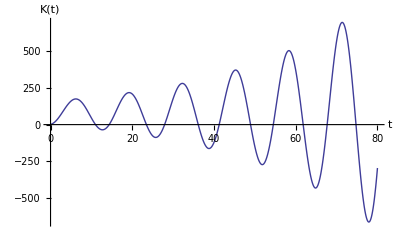

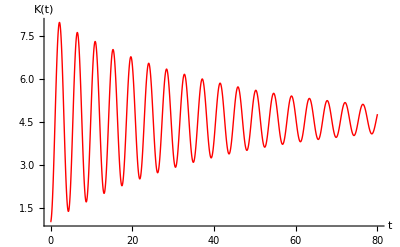

```mathematica
ClearAll;
a=0.95;
b=0.12;
τ=1;
m:=1;
upto=80;
A[t_]:=0;
Ca[t_]:=10;
ϵ[t_]:=0;
ArcCos[a/(a+b*τ)]
Sqrt[b *τ*(b*τ+2*a) ]
f[x_[t_]]:=x'[t]-a/τ*x[t] +(a/τ+b)*x[t-τ]-a(A[t-τ]+Ca[t-τ]+ϵ[t-τ]);
ff[x_[t_]]:=Sum[(τ^(n-1)/Factorial[n-1])*D[x[t],{t,n}],{n,m+1}]-a/τ*Sum[(τ^(n)/Factorial[n])*D[x[t],{t,n}],{n,m}]+x[t] +(a/τ+b)*x[t]-a(A[t]+Ca[t]+ϵ[t]);
init:={};
For[i=m,i≥1,i--,
PrependTo[init,(D[x[t],{t,i}]==0)/.{t->0}]
]
PrependTo[init,x[0]==1];
s:=NDSolve[{f[x[t]]==0,x[t/;t<0]==1},x,{t,0,upto}];
ss:=NDSolve[{ff[x[t]]==0,x[t/;t<0]==1},x,{t,-τ,upto}];
Plot[Evaluate[x[t]/.s],{t,0,upto},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t","K(t)"}]
Plot[Evaluate[x[t]/.ss],{t,0,upto},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t","K(t)"},PlotStyle->Red]
```